# Cycle work of an open quantum three-level system

## General definitions

```mathematica
(*Define the 8 Gell-Mann Matrices (Generators of SU(3))*)
gm[1]={{0,1,0},{1,0,0},{0,0,0}};
gm[2]={{0,-I,0},{I,0,0},{0,0,0}};
gm[3]={{1,0,0},{0,-1,0},{0,0,0}};
gm[4]={{0,0,1},{0,0,0},{1,0,0}};
gm[5]={{0,0,-I},{0,0,0},{I,0,0}};
gm[6]={{0,0,0},{0,0,1},{0,1,0}};
gm[7]={{0,0,0},{0,0,-I},{0,I,0}};
gm[8]=1/Sqrt[3]*{{1,0,0},{0,1,0},{0,0,-2}};
id=IdentityMatrix[3];

(*Define a helper function for the Lindblad Dissipator*)
LindbladDissipator[L_,p_]:=L.p.ConjugateTranspose[L]-1/2*(ConjugateTranspose[L].L.p+p.ConjugateTranspose[L].L)

(*Define Bose-Einstein distribution*)
(*We set hbar=kB=1 for symbolic simplicity*)
nBE[omega_,T_]:=1/(Exp[omega/T]-1);

(* Find steady state module *)
ClearAll[GetSteadyState];
GetSteadyState[hamiltonian_,dissipatorFunction_]:=Module[{v,rho,Lrho,eqs,vars,sol},
(*Bloch Vector Representation*)
rho=1/3*id+1/2*Sum[v[k]*gm[k],{k,1,8}];
vars=Table[v[k],{k,1,8}];
(*Construct Master Equation:-i[H,rho]+D(rho)*)
(*dissipatorFunction is applied to the symbolic rho*)
Lrho=-I*(hamiltonian.rho-rho.hamiltonian)+dissipatorFunction[rho];
(*Formulate Real/Imaginary Equations*)eqs=Join[Thread[Flatten[ComplexExpand[Re[Lrho]]]==0],Thread[Flatten[ComplexExpand[Im[Lrho]]]==0]];
(*Solve and Reconstruct*)
sol=Solve[eqs,vars];
If[sol==={},Print["Warning: No steady state found! Check your dissipators."];Return[Null],FullSimplify[rho/. sol[[1]]]]];

ClearAll[AnalyzeGeometricHeat];
AnalyzeGeometricHeat[ham_,rhoSS_,dissipatorFunc_,params_,ranges_,gammaRules_]:=
Module[{Ai,n,F,plotExpr},

(*3. Calculate Heat One-Form Components Ai=Tr[H.d_i(rhoSS)]*)
Ai=Table[Tr[ham.D[rhoSS,p]],{p,params}];

(*4. Calculate Curvature Matrix Fij=d_i Aj-d_j Ai*)
n=Length[params];
F=Table[D[Ai[[j]],params[[i]]]-D[Ai[[i]],params[[j]]],{i,n},{j,n}]//Simplify;

(*5. Prepare Plot*)
(*We plot F[[1,2]] which is the fundamental curvature for a 2D parameter space*)plotExpr=ComplexExpand[Re[F[[1,2]]]]/. gammaRules;

ContourPlot[
plotExpr,
ranges[[1]],
ranges[[2]],
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
Contours->25,
AxesLabel->{params[[2]],params[[1]]},
PlotLabel->"Geometric Heat Curvature Map",
FrameLabel->{params[[2]],params[[1]]}]

];
```

### Plot Liouvillian Gap

```mathematica
ClearAll[PlotLiouvillianGap];

PlotLiouvillianGap[ham_,dissipatorFunc_,params_,ranges_,rules_:{}]:=Module[{basis,liouvillianMatrix,applyL,matrixL,evals,gapFunc,plotExpr},
(*1. Create a basis of 3x3 matrices to vectorize the operator*)basis=Flatten[Table[ReplacePart[0 id,{i,j}->1],{i,3},{j,3}],1];

(*2. Define the action of the Liouvillian on a matrix rho*)
applyL[rho_]:=-I*(ham.rho-rho.ham)+dissipatorFunc[rho];

(*3. Construct the 9x9 Liouvillian Matrix*)
(*Each column is the vectorized result of L acting on a basis element*)matrixL=Table[Flatten[applyL[b]],{b,basis}]//Transpose;

(*4. Define the Gap Calculation*)
(*We find the eigenvalue with the smallest non-zero real part*)gapFunc[p1_,p2_]:=Module[{numL,eigs,nonZeroEigs},
numL=matrixL/. Thread[params->{p1,p2}]/. rules;
eigs=Eigenvalues[numL];

(*Filter out the zero eigenvalue (steady state)*)
nonZeroEigs=Select[eigs,Abs[#]>10^-10&];
If[Length[nonZeroEigs]==0,0,Min[Abs[Re[nonZeroEigs]]]]];

(*5. Generate Plot*)
Print["--- Generating Liouvillian Gap Map ---"];
ContourPlot[gapFunc[params[[1]],params[[2]]],ranges[[1]],ranges[[2]],ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->20,AxesLabel->{params[[1]],params[[2]]},PlotLabel->"Liouvillian Spectral Gap",Exclusions->None 
(*Ensures we see where it hits zero*)]];
```

### Compare reversible and dissipative heat Q_diss=-∫dt g_ij dλ^i/dt dλ^j/dt

```mathematica
ClearAll[ComputeCycleHeats];
ComputeCycleHeats[rhoSS_,ham_,dissipatorFunc_,params_,ranges_,rules_,R_,offset_,tau_:2 Pi]:=Module[{dRho,solveLInv,gMetric,Ai,path,dPath,integrandGeo,integrandDiss,qGeo,qDiss,varsX,basis},

Ai=Table[Tr[ham.D[rhoSS,p]],{p,params}];
dRho=Table[D[rhoSS,p],{p,params}];

solveLInv[target_]:=Module[{X,x,varsX,eqsL,solX},
varsX=Table[x[k],{k,1,8}];
X=Sum[varsX[[k]]*gm[k],{k,1,8}];
eqsL=Thread[Flatten[-I*(ham.X-X.ham)+dissipatorFunc[X]]==Flatten[target]];
solX=Solve[eqsL,varsX];
If[solX==={},0,X/. solX[[1]]]];

gMetric=Table[Tr[dRho[[i]].solveLInv[dRho[[j]]]],{i,2},{j,2}];
path={R*Cos[t]+offset[[1]],R*Sin[t]+offset[[2]]};
dPath=D[path,t];

integrandGeo=(Ai/. Thread[params->path]).dPath;
integrandDiss=(dPath.(gMetric/. Thread[params->path]).dPath);
qGeo=NIntegrate[integrandGeo/. rules,{t,0,2 Pi}];
qDiss=-(1/tau)*NIntegrate[integrandDiss/. rules,{t,0,2 Pi}];

Print["--- Cycle Results (tau = ",tau,") ---"];
Print["Geometric Heat (Reversible): ",qGeo];
Print["Dissipated Heat (Irreversible): ",qDiss];
Print["Net Heat: ",qGeo+qDiss];
{qGeo,qDiss}
];
```

## Example 1: Rubidium atom

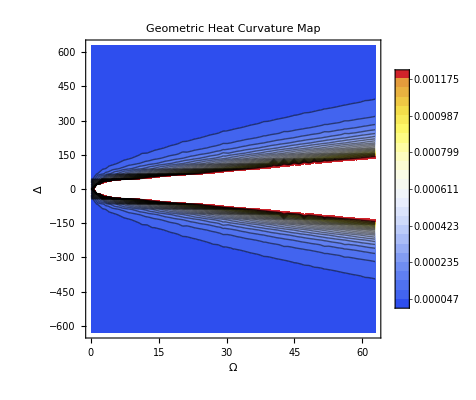

```mathematica
(*
Δ=2π [-100,100] MHz, Ω=2π [0,10] MHz, Subscript[γ, diss]=2π 6.1 MHz, Subscript[γ, ϕ]=1 MHz, 
*)
H3=({{0, 0, Ω1/2}, {0, Δ1, Ω2/2}, {Ω1/2, Ω2/2, Δ2}})/.{Ω1->Ω,Ω2->Ω, Δ2->Δ,Δ1->Δ/10};

Dissipators3=Function[r,γdiss*LindbladDissipator[({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}),r]+γdiss*LindbladDissipator[({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}}),r]+γϕ*LindbladDissipator[({{0, 0, 0}, {0, 1, 0}, {0, 0, -1}}),r]+γϕ*LindbladDissipator[({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}}),r]];
rhoSS=GetSteadyState[H3,Dissipators3]/.{Ω1->Ω,Ω2->Ω, Δ2->Δ,Δ1->Δ/10};
AnalyzeGeometricHeat[H3,rhoSS,Dissipators3,{Δ,Ω},{{Ω,0.1,2π 10},{Δ,-2π 100,2π 100}},{γdiss->2 π 6.1,γϕ->1}]
```

--- Generating Liouvillian Gap Map ---

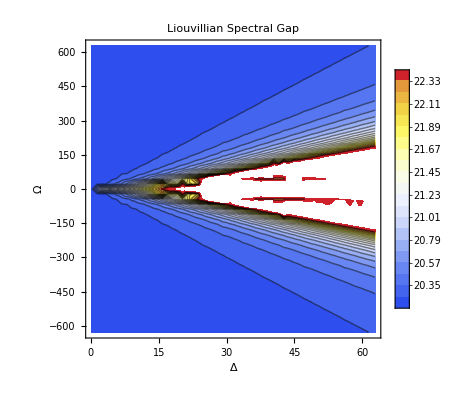

```mathematica
PlotLiouvillianGap[H3,Dissipators3,{Δ,Ω},{{Ω,0.1,2π 10},{Δ,-2π 100,2π 100}},{γdiss->2 π 6.1,γϕ->1}]
```

```mathematica
results=ComputeCycleHeats[
rhoSS,(*The symbolic state*)
H3,(*The Hamiltonian*)
Dissipators3,(*The dissipator function*)
{Δ,Ω},(*{Δ,Ω}*)
{},(*Ranges (unused in integration, but kept for signature)*)
{γdiss->2 π 6.1,γϕ->1},(*Numerical value for γ in MHz*)
50,(*Radius R in MHz*)
{40.0,200},(*Offset for params in MHz*)
200.0   (*Period τ in 0.159 μs, should be >> than L. gap*)];
(*The result unit correspond to around 7 mK in temperature*)
```

--- Cycle Results (tau = 200.) ---

Geometric Heat (Reversible): 12.0101

Dissipated Heat (Irreversible): 4.56879×10^-6-2.72007×10^-21 ⅈ

Net Heat: 12.0101-2.72007×10^-21 ⅈ

## Example 2: The Scovil-Schulz-DuBois (SSDB) Maser

--- Steady state ---

(1/3 | 0 | 0
0 | 1/3 | 0
0 | 0 | 1/3)

--- Curvature Matrix (F_ij) ---

(0 | 0
0 | 0)

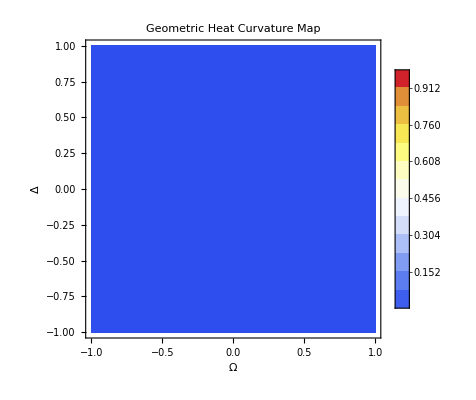

```mathematica
H=(E1*id+(E2-E1)*gm[3]+(E3-E1)*gm[8]+Omega*(gm[6]))/.{E3->Δ,E2->Δ/2,E1->0}; 

HotDown={{0,0,1},{0,0,0},{0,0,0}}; 
HotUp=ConjugateTranspose[HotDown];     
ColdDown={{0,1,0},{0,0,0},{0,0,0}}; 
ColdUp=ConjugateTranspose[ColdDown];

Dissipators=Function[r,γh*LindbladDissipator[HotDown,r]+γh*LindbladDissipator[HotUp,r]+γc*LindbladDissipator[ColdDown,r]+γc*LindbladDissipator[ColdUp,r]];

rhoSS=GetSteadyState[H,Dissipators];
Print["--- Steady state ---"];
rhoSS//MatrixForm
AnalyzeGeometricHeat[H,rhoSS,Dissipators,{Δ,Ω},{{Ω,-1,1},{Δ,-1,1}},{γh->0.1,γc->0.1}]
```

## Example 3: The Quantum Absorption Refrigerator

```mathematica
(*Jump operators for the three reservoirs*)
ColdDown={{0,1,0},{0,0,0},{0,0,0}};
ColdUp={{0,0,0},{0,1,0},{0,0,0}};
WorkDown={{0,0,0},{0,0,1},{0,0,0}};
WorkUp={{0,0,0},{0,0,0},{0,1,0}};
HotDown={{0,0,1},{0,0,0},{0,0,0}};
HotUp={{0,0,0},{0,0,0},{1,0,0}};
nc = nBE[Δ1-Δ2,Tc]/.{Δ1->Δ,Δ2->Δ/2,Tc->1.0};
nw = nBE[Δ2,Tw]/.{Δ1->Δ,Δ2->Δ/2,Tw->2.0};
nh=nBE[Δ1,Th]/.{Δ1->Δ,Δ2->Δ/2,Th->2.0};
(*In the master equation,you'd add terms for each with rates proportional to the Bose-Einstein distribution n_B(T) and n_B(T)+1*)

H=({{0, 0, Ω1/2}, {0, Δ1-Δ2, Ω2/2}, {Ω1/2, Ω2/2, Δ1}})/.{Ω1->Ω,Ω2->Ω, Δ1->Δ,Δ2->Δ/2};

DissCold=Function[r,γc*(nc+1)*LindbladDissipator[ColdDown,r]+γc*nc*LindbladDissipator[ColdUp,r]];
DissHot=Function[r,γh*(nh+1)*LindbladDissipator[HotDown,r]+γh*nh*LindbladDissipator[HotUp,r]];
DissWork=Function[r,γw*(nw+1)*LindbladDissipator[WorkDown,r]+γw*nw*LindbladDissipator[WorkUp,r]];

Dissipators =Function[r,( DissCold[r] + DissHot[r ]+ DissWork[r])/.{γc->γ,γh->γ,γw->γ}];

rhoSS=GetSteadyState[H,Dissipators];
Print["--- Steady state ---"];
rhoSS//MatrixForm
AnalyzeGeometricHeat[H,rhoSS,Dissipators,{Δ,Ω},{{Ω,-1,1},{Δ,-1,1}},{γ->0.1}]
```

Warning: No steady state found! Check your dissipators.

--- Steady state ---

Null

-Graphics-

```mathematica
(*7. Calculate Heat Currents:J=Tr[H*D(rho)]*)
Jcold=Tr[H.DissCold[rhoSS]]//Simplify;
Jhot=Tr[H.DissHot[rhoSS]]//Simplify;

(*Work Power:P=-(J_hot+J_cold)*)
PowerOut=-(Jhot+Jcold)//Simplify;

(*Efficiency:eta=Power/Heat_In*)
efficiency=PowerOut/Jhot//Simplify
```

-1-Tr[{{0,0,Ω/2},{0,Δ/2,Ω/2},{Ω/2,Ω/2,Δ}}.(-1/(2 (-1+ⅇ^(0.5 Δ)))γc ((1+ⅇ^(0.5 Δ)) Null.{{0,0,0},{0,1,0},{0,0,0}}+(1+ⅇ^(0.5 Δ)) {{0,0,0},{0,1,0},{0,0,0}}.Null-2 ({{0,0,0},{0,1,0},{0,0,0}}.Null.{{0,0,0},{0,1,0},{0,0,0}}+ⅇ^(0.5 Δ) {{0,1,0},{0,0,0},{0,0,0}}.Null.{{0,0,0},{1,0,0},{0,0,0}})))]/Tr[{{0,0,Ω/2},{0,Δ/2,Ω/2},{Ω/2,Ω/2,Δ}}.(-1/(2 (-1+ⅇ^(0.5 Δ)))γh (ⅇ^(0.5 Δ) Null.{{0,0,0},{0,0,0},{0,0,1}}+Null.{{1,0,0},{0,0,0},{0,0,0}}+ⅇ^(0.5 Δ) {{0,0,0},{0,0,0},{0,0,1}}.Null+{{1,0,0},{0,0,0},{0,0,0}}.Null-2 {{0,0,0},{0,0,0},{1,0,0}}.Null.{{0,0,1},{0,0,0},{0,0,0}}-2 ⅇ^(0.5 Δ) {{0,0,1},{0,0,0},{0,0,0}}.Null.{{0,0,0},{0,0,0},{1,0,0}}))]

## Example 4: Collective-mode BEC in an optical trap

(0 | F | 0
F | Ω | √2 F
0 | √2 F | U+2 Ω)

rhoSS: ((4 (36 F^6 (2 γc+γh)^2+2 F^4 (4 U^2 γc (14 γc+15 γh)+9 (2 γc+γh) (12 γc^3+20 γc^2 γh+8 γc γh^2+γh^3)+24 U γc (6 γc+7 γh) Ω+4 (22 γc^2+29 γc γh+γh^2) Ω^2)+γc^2 ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+F^2 γc (8 U^4 (2 γc+3 γh)+9 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^2+16 γc γh+3 γh^2)+16 U^3 (6 γc+7 γh) Ω+2 (448 γc^3+552 γc^2 γh+312 γc γh^2+217 γh^3) Ω^2+32 (10 γc+γh) Ω^4+4 U Ω (248 γc^3+320 γc^2 γh+172 γc γh^2+109 γh^3+24 (5 γc+γh) Ω^2)+2 U^2 (144 γc^3+236 γc^2 γh+116 γc γh^2+57 γh^3+12 (12 γc+7 γh) Ω^2))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))) | (4 ⅈ F (2 γc-γh) (6 F^4 (2 γc+γh) (4 ⅈ U+6 γc+3 γh+6 ⅈ Ω)+γc (U+3 ⅈ (γc+γh)+Ω) (2 U-ⅈ (4 γc+γh)+4 Ω) (2 U+ⅈ (4 γc+γh)+4 Ω) (-3 ⅈ (2 γc^2+γc γh+γh^2)+U (2 γc+3 γh+2 ⅈ Ω)+(8 γc+5 γh) Ω+2 ⅈ Ω^2)+F^2 (16 ⅈ U^3 γc+9 (2 γc+γh) (4 γc+γh) (4 γc^2+3 γc γh+γh^2)+6 ⅈ U (24 γc^3+20 γc^2 γh+8 γc γh^2+3 γh^3)+4 U^2 γc (18 γc+9 γh+26 ⅈ Ω)+8 U γc (26 γc+11 γh) Ω+6 ⅈ (3 γc+2 γh) (16 γc^2+4 γc γh+3 γh^2) Ω+4 (4 γc+γh) (10 γc+γh) Ω^2+8 ⅈ U (28 γc+γh) Ω^2+16 ⅈ (10 γc+γh) Ω^3)))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))) | -(2 √2 F^2 (2 γc-γh) ((2 U-ⅈ (4 γc+γh)+4 Ω) (4 U γc+12 ⅈ γc^2+6 ⅈ γc γh-3 ⅈ γh^2+4 γc Ω-2 γh Ω) (6 γc^2+3 γc γh+3 γh^2+ⅈ U (2 γc+3 γh+2 ⅈ Ω)+8 ⅈ γc Ω+5 ⅈ γh Ω-2 Ω^2)-2 F^2 (4 U^2 (2 γc-3 γh)+9 (-8 γc^3-8 γc^2 γh+γh^3)-18 ⅈ (4 γc-γh) (2 γc+γh) Ω+12 (6 γc-γh) Ω^2+2 U (2 γc-γh) (-9 ⅈ (2 γc+γh)+14 Ω))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2)))
-(4 F (2 γc-γh) (6 F^4 (2 γc+γh) (4 U+3 ⅈ (2 γc+γh)+6 Ω)+γc (ⅈ U+3 (γc+γh)+ⅈ Ω) (2 U-ⅈ (4 γc+γh)+4 Ω) (2 U+ⅈ (4 γc+γh)+4 Ω) (3 ⅈ (2 γc^2+γc γh+γh^2)+U (2 γc+3 γh-2 ⅈ Ω)+(8 γc+5 γh) Ω-2 ⅈ Ω^2)+F^2 (16 U^3 γc+9 ⅈ (2 γc+γh) (4 γc+γh) (4 γc^2+3 γc γh+γh^2)+6 U (24 γc^3+20 γc^2 γh+8 γc γh^2+3 γh^3)+8 ⅈ U γc (26 γc+11 γh) Ω+6 (3 γc+2 γh) (16 γc^2+4 γc γh+3 γh^2) Ω+4 ⅈ (4 γc+γh) (10 γc+γh) Ω^2+8 U (28 γc+γh) Ω^2+16 (10 γc+γh) Ω^3+4 U^2 γc (9 ⅈ (2 γc+γh)+26 Ω))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))) | (2 (72 F^6 (2 γc+γh)^2+2 F^4 (8 U^2 (18 γc^2+7 γc γh+3 γh^2)+9 (2 γc+γh) (32 γc^3+28 γc^2 γh+18 γc γh^2+3 γh^3)+16 U (26 γc^2+7 γc γh+5 γh^2) Ω+4 (80 γc^2+10 γc γh+17 γh^2) Ω^2)+γc γh ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+F^2 (16 U^4 γc (2 γc+3 γh)+9 (4 γc+γh) (2 γc^2+γc γh+γh^2) (16 γc^3+20 γc^2 γh+10 γc γh^2+γh^3)+32 U^3 γc (6 γc+7 γh) Ω+4 (320 γc^4+496 γc^3 γh+342 γc^2 γh^2+158 γc γh^3+37 γh^4) Ω^2+64 (γc+γh) (2 γc+γh) Ω^4+16 U Ω (88 γc^4+142 γc^3 γh+95 γc^2 γh^2+41 γc γh^3+9 γh^4+2 (4 γc+γh) (3 γc+2 γh) Ω^2)+4 U^2 (104 γc^4+192 γc^3 γh+130 γc^2 γh^2+48 γc γh^3+9 γh^4+4 (26 γc^2+24 γc γh+γh^2) Ω^2))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))) | (ⅈ √2 F (2 γc-γh) (24 F^4 (2 γc+γh) (4 ⅈ U+6 γc+3 γh+6 ⅈ Ω)+γh (6 γc+3 γh-2 ⅈ Ω) (2 ⅈ U+4 γc+γh+4 ⅈ Ω) (2 U+ⅈ (4 γc+γh)+4 Ω) (-3 ⅈ (2 γc^2+γc γh+γh^2)+U (2 γc+3 γh+2 ⅈ Ω)+(8 γc+5 γh) Ω+2 ⅈ Ω^2)+2 F^2 (8 ⅈ U^3 (2 γc+3 γh)+9 (2 γc+γh) (4 γc+γh) (4 γc^2+4 γc γh+3 γh^2)+6 ⅈ (48 γc^3+88 γc^2 γh+40 γc γh^2+9 γh^3) Ω+4 (8 γc^2-2 γc γh+17 γh^2) Ω^2+16 ⅈ (2 γc+5 γh) Ω^3+8 U^2 (4 γc^2+4 γc γh+3 γh^2+8 ⅈ γc Ω+13 ⅈ γh Ω)+4 U (3 ⅈ (2 γc+3 γh) (6 γc^2+4 γc γh+γh^2)+4 (4 γc^2+3 γc γh+5 γh^2) Ω+2 ⅈ (10 γc+19 γh) Ω^2))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2)))
(2 √2 F^2 (2 γc-γh) ((2 U+ⅈ (4 γc+γh)+4 Ω) (4 ⅈ U γc+12 γc^2+6 γc γh-3 γh^2+4 ⅈ γc Ω-2 ⅈ γh Ω) (3 ⅈ (2 γc^2+γc γh+γh^2)+U (2 γc+3 γh-2 ⅈ Ω)+(8 γc+5 γh) Ω-2 ⅈ Ω^2)+2 F^2 (4 U^2 (2 γc-3 γh)+9 (-8 γc^3-8 γc^2 γh+γh^3)+18 ⅈ (4 γc-γh) (2 γc+γh) Ω+12 (6 γc-γh) Ω^2+2 U (2 γc-γh) (9 ⅈ (2 γc+γh)+14 Ω))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))) | -(√2 F (2 γc-γh) (24 F^4 (2 γc+γh) (4 U+3 ⅈ (2 γc+γh)+6 Ω)+γh (6 γc+3 γh+2 ⅈ Ω) (2 U-ⅈ (4 γc+γh)+4 Ω) (2 U+ⅈ (4 γc+γh)+4 Ω) (3 ⅈ (2 γc^2+γc γh+γh^2)+U (2 γc+3 γh-2 ⅈ Ω)+(8 γc+5 γh) Ω-2 ⅈ Ω^2)+2 F^2 (8 U^3 (2 γc+3 γh)+9 ⅈ (2 γc+γh) (4 γc+γh) (4 γc^2+4 γc γh+3 γh^2)+6 (48 γc^3+88 γc^2 γh+40 γc γh^2+9 γh^3) Ω+4 ⅈ (8 γc^2-2 γc γh+17 γh^2) Ω^2+16 (2 γc+5 γh) Ω^3+8 U^2 (4 ⅈ γc^2+4 ⅈ γc γh+3 ⅈ γh^2+8 γc Ω+13 γh Ω)+4 U (3 (2 γc+3 γh) (6 γc^2+4 γc γh+γh^2)+4 ⅈ (4 γc^2+3 γc γh+5 γh^2) Ω+2 (10 γc+19 γh) Ω^2))))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))) | (144 F^6 (2 γc+γh)^2+16 F^4 ((2 γc+γh) (U^2 (4 γc+9 γh)+9 (4 γc^3+7 γc^2 γh+5 γc γh^2+γh^3))+4 U (4 γc^2+14 γc γh+7 γh^2) Ω+(8 γc^2+34 γc γh+23 γh^2) Ω^2)+γh^2 ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+2 F^2 γh (8 U^4 (2 γc+3 γh)+9 (4 γc+γh) (2 γc^2+γc γh+γh^2) (16 γc^2+12 γc γh+3 γh^2)+64 U^3 (γc+2 γh) Ω+2 (640 γc^3+672 γc^2 γh+408 γc γh^2+115 γh^3) Ω^2+128 (γc+γh) Ω^4+U^2 (352 γc^3+456 γc^2 γh+296 γc γh^2+78 γh^3+96 γc Ω^2+264 γh Ω^2)+4 U Ω (288 γc^3+356 γc^2 γh+232 γc γh^2+65 γh^3+4 (8 γc+17 γh) Ω^2)))/(432 F^6 (2 γc+γh)^2+12 F^4 ((2 γc+γh) (4 U^2 (12 γc+5 γh)+9 (24 γc^3+32 γc^2 γh+18 γc γh^2+3 γh^3))+32 U (8 γc^2+7 γc γh+2 γh^2) Ω+8 (22 γc^2+17 γc γh+7 γh^2) Ω^2)+(4 γc^2+2 γc γh+γh^2) ((4 γc+γh)^2+4 (U+2 Ω)^2) (9 (2 γc^2+γc γh+γh^2)^2+(40 γc^2+68 γc γh+13 γh^2) Ω^2+4 Ω^4+2 U Ω (4 γc^2+28 γc γh+9 γh^2+4 Ω^2)+U^2 ((2 γc+3 γh)^2+4 Ω^2))+4 F^2 (4 U^4 (4 γc+γh) (2 γc+3 γh)+18 (4 γc+γh) (2 γc^2+γc γh+γh^2) (8 γc^3+17 γc^2 γh+7 γc γh^2+γh^3)+64 U^3 (γc+γh) (3 γc+γh) Ω+3 (512 γc^4+912 γc^3 γh+660 γc^2 γh^2+386 γc γh^3+63 γh^4) Ω^2+96 (4 γc^2+2 γc γh+γh^2) Ω^4+2 U Ω (848 γc^4+1496 γc^3 γh+1080 γc^2 γh^2+614 γc γh^3+101 γh^4+84 (4 γc^2+2 γc γh+γh^2) Ω^2)+U^2 (496 γc^4+1032 γc^3 γh+720 γc^2 γh^2+358 γc γh^3+57 γh^4+4 (124 γc^2+102 γc γh+35 γh^2) Ω^2))))

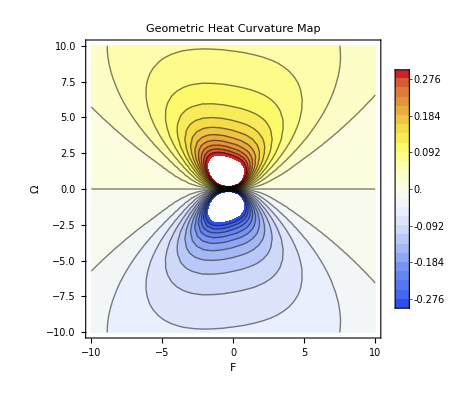

```mathematica
AnnihilationOp[n_]:=DiagonalMatrix[Sqrt[Range[n-1]],1];
CreationOp[n_]:=ConjugateTranspose[AnnihilationOp[n]];

a=AnnihilationOp[3];
adag=ConjugateTranspose[a];

HBEC=Ω*(adag.a)+(U/2)*(adag.adag.a.a)+F*(adag+a);
Print[HBEC//MatrixForm]

nc =1;
LCool[r_]:=γc*(nc+1)*LindbladDissipator[a,r];
LHeat[r_]:=γh*nc*LindbladDissipator[adag,r];
L3Body[r_]:=γ3*LindbladDissipator[a.a.a,r];

FullLindbladian[r_]:=LCool[r]+LHeat[r]+L3Body[r];

rhoSS=GetSteadyState[HBEC,FullLindbladian];
Print["rhoSS: ",rhoSS//MatrixForm]
AnalyzeGeometricHeat[HBEC,rhoSS,FullLindbladian,{Ω,F},{{Ω,-10, 10},{F,-10,10}},{U->1,γ3->1,γh->1,γc->1}]
```

## Example 5: Motion-TLS coupled system

```mathematica
AnnihilationOp[n_]:=DiagonalMatrix[Sqrt[Range[n-1]],1];
CreationOp[n_]:=ConjugateTranspose[AnnihilationOp[n]];
Needs["Pauli`"];

Nmot = 3;
a=AnnihilationOp[Nmot];
adag=ConjugateTranspose[a];
mF =({{2, 0}, {0, 1}});
σup=(σ[1]+I*σ[2])/2;
xh0 = √(1/2m*ω);
η=(μB*xho*dB)/2/.{μB->1,dB->1};

(* Define the Hamiltonian *)
Hmot = σ[0]⊗(ω*(adag.a)-ω*x0/xho*(adag+a));
Hspin = (Δ*σ[3]+Ω*σ[1])⊗IdentityMatrix[Nmot];
Hcoup =mF⊗(η*(adag+a));
Htot=FullSimplify[Hmot+Hspin+Hcoup];

(* Define the dissipator *)
LOP[r_]:=LindbladDissipator[√γup*σup⊗IdentityMatrix[Nmot],r];
LDP[r_]:=LindbladDissipator[√(γϕ/2)*σ[3]⊗IdentityMatrix[Nmot],r];
LC[r_]:=LindbladDissipator[√(Γm*(n+1))*σ[0]⊗a,r];
LH[r_]:=LindbladDissipator[√(Γm*n)*σ[0]⊗adag,r];
FullLindbladian[r_]:=LOP[r]+LDP[r]+LC[r]+LH[r];

(* Compute steady state and heat curvature *)
rhoSS=GetSteadyState[Htot,FullLindbladian];
Print["rhoSS: ",rhoSS//MatrixForm]
AnalyzeGeometricHeat[Htot,rhoSS,FullLindbladian,
{x0,ω},{{x0,-10, 10},{ω,0,10}},{γup->1,γϕ->1,Γm->1,n->1,m->1}]
```